```mathematica
$Post = MatrixForm;
(*derive the projectile's position as a function of time*)
R2 = 120;
vInitial = {Vx,Vy} +  r0*omega*{-Sin[omega*t0-Pi/2],Cos[omega *t0 - Pi/2]};
p = vInitial * t + {0,-R};
startingValues = {Vx->1,Vy->1,r0->100,t0 -> 0,omega -> .01,R->105};
path[t_] = p /. startingValues
Thrower[t_] = R{-Sin[omega*t-Pi/2],Cos[omega *t - Pi/2]}/.startingValues
```

Null

Null

Null

«2 more identical outputs»

(2. t
-105+1. t)

(105 Cos[0.01 t]
105 Sin[0.01 t])

Null

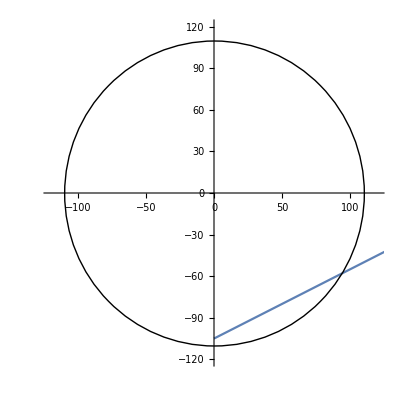

```mathematica
(*This is what our setup looks like. A ball is thrown at the bottom of the ship*)
parametric = ParametricPlot[{{1,0}.path[t],{0,1}.path[t]},{t,0,100},PlotRange->{{-R2,R2},{-R2,R2}}];
Show[ parametric,Graphics[Circle[{0,0},110]],PlotRangeClipping->True]
```

```mathematica
(*pvec is a vector that points to the ball from ship center*)
(*Thus distance from center is given by*)
rMag[t_] = Sqrt[path[t].path[t]];
angleInRads[t_]= VectorAngle[({{2. t}, {-110+1. t}}),({{110 Cos[0.01 t]}, {110 Sin[0.01 t]}})]
```

Null

Set::write: Tag ArcCos in ArcCos[(220. t Cos[0.01 Conjugate[t]]+110 (-110+1. t) Sin[0.01 Conjugate[t]])/(√(4. Abs[t]^2+Abs[-110+Times[«2»]]^2) √(12100 Abs[Cos[«1»]]^2+12100 Abs[Sin[«1»]]^2))][t_] is Protected.

ArcCos[(220. t Cos[0.01 Conjugate[t]]+110 (-110+1. t) Sin[0.01 Conjugate[t]])/(√(4. Abs[t]^2+Abs[-110+1. t]^2) √(12100 Abs[Cos[0.01 t]]^2+12100 Abs[Sin[0.01 t]]^2))]

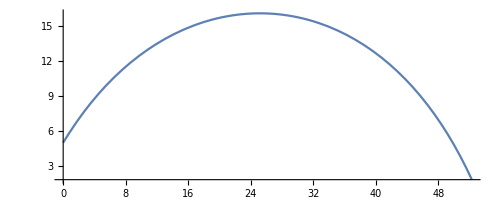

```mathematica
ParametricPlot[{110*((220. t Cos[0.01 Conjugate[t]]+110 (-110+1. t) Sin[0.01 Conjugate[t]])/(√(4. Abs[t]^2+Abs[-110+1. t]^2) √(12100 Abs[Cos[0.01 t]]^2+12100 Abs[Sin[0.01 t]]^2))),110 - rMag[t]},{t,0,45}]
```